```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

### Setting up the mean field and the matrix f and G

```mathematica
mfsols=Simplify[Solve[-mup+λ*np*phip^(np-2)*phim^nm*phi0^n0 Vp^(2V-4)*Vp^(np-1)*V0^n0*Vm^nm==0&&-mu0+λ*n0*phip^np*phim^nm*phi0^(n0-2)Vp^(2V-4)*Vp^np*V0^(n0-1)*Vm^nm==0&&-mum+λ*nm*phip^np*phim^(nm-2)*phi0^n0 Vp^(2V-4)*Vp^np*V0^n0*Vm^(nm-1)==0,{phip,phi0,phim}],np+n0+nm==V&&mup>0&&mu0>0&&mum>0&&Vp>0&&V0>0&&Vm>0&&V>0&&np>0&&n0>0&&nm>0&&Element[{Vp,V0,Vm,np,nm,n0,mup,mu0,mum,V},Reals]][[1]]
Simplify[PowerExpand[Vp*λ*((phip/.mfsols[[1]])*Vp)^(np-2)*((phi0/.mfsols[[2]])*V0)^n0*((phim/.mfsols[[3]])*Vm)^nm],np+n0+nm==V&&mup>0&&mu0>0&&mum>0&&Vp>0&&V0>0&&Vm>0&&V>0&&np>0&&n0>0&&nm>0&&Element[{Vp,V0,Vm,np,nm,n0,mup,mu0,mum,V},Reals]]
```

{phip→-((mu0 mum)/(V0 Vm))^(1/4)/(Vp^3 √λ),phi0→-((mum/(mu0 V0^3 Vm))^(1/4))/(√2 √((Vp^5 λ)/mup)),phim→-((mu0/(mum V0 Vm^3))^(1/4))/(√2 √((Vp^5 λ)/mup))}

mup/(2 Vp^4)

```mathematica
Phiplus=(-mup/(λ*np))^((2+np-V)/(2(V-2)))*(-mu0/(λ*n0))^(n0/(2(V-2)))*(-mum/(λ*nm))^(nm/(2(V-2)))*Vp^(-(2V-4)/(V-2))*Vp^(-np/(2(V-2))-1/2)*V0^(-n0/(2(V-2)))*Vm^(-nm/(2(V-2)));
Phi0=(-mu0/(λ*n0))^((2+n0-V)/(2(V-2)))*(-mup/(λ*np))^(np/(2(V-2)))*(-mum/(λ*nm))^(nm/(2(V-2)))*Vp^(-(2V-4)/(V-2))*Vp^(-np/(2(V-2)))*V0^(-n0/(2(V-2))-1/2)*Vm^(-nm/(2(V-2)));
Phiminus=(-mum/(λ*nm))^((2+nm-V)/(2(V-2)))*(-mu0/(λ*n0))^(n0/(2(V-2)))*(-mup/(λ*np))^(np/(2(V-2)))*Vp^(-(2V-4)/(V-2))*Vp^(-np/(2(V-2)))*V0^(-n0/(2(V-2)))*Vm^(-nm/(2(V-2))-1/2);
(*Here, there are factors of Vp missing from empty group integrations when doing the linearization. Volume factors go into Subscript[chi, ab] such that reg. works*)
```

```mathematica
fpp=Simplify[PowerExpand[Vp*λ*(Phiplus*Vp)^(np-2)*(Phi0*V0)^n0*(Phiminus*Vm)^nm],np+n0+nm==V]
fmm=Simplify[PowerExpand[Vm*λ*(Phiminus*Vm)^(nm-2)*(Phi0*V0)^n0*(Phiplus*Vp)^np],np+n0+nm==V]
f00=Simplify[PowerExpand[V0*λ*(Phi0*V0)^(n0-2)*(Phiminus*Vm)^nm*(Phiplus*Vp)^np],np+n0+nm==V]
fpm=Simplify[PowerExpand[Vp*λ*(Phiminus*Vm)^(nm-1)*(Phi0*V0)^n0*(Phiplus*Vp)^(np-1)],np+n0+nm==V]
fmp=Simplify[PowerExpand[Vm*λ*(Phiminus*Vm)^(nm-1)*(Phi0*V0)^n0*(Phiplus*Vp)^(np-1)],np+n0+nm==V]
```

-(mup Vp^(4-2 V))/np

-(mum Vp^(4-2 V))/nm

-(mu0 Vp^(4-2 V))/n0

-(√mum √mup Vp^(9/2-2 V))/(√nm √np √Vm)

-(√mum √mup √Vm Vp^(7/2-2 V))/(√nm √np)

### Local correlator: diagonal components

```mathematica
Clear[χ,G]
G3sign[k_,Cas_,mup_,mu0_,mum_,np_,n0_,nm_,χ_,A1_,A2_,A3_,B1_,B2_,B3_]:={{B1(4Cas)/a^2+A1*k^2+mup(1-χ[[1,1]]/np),-Sqrt[(mup*mu0)/(np*n0)]χ[[1,2]],-Sqrt[(mup*mum)/(np*nm)]χ[[1,3]]},{-Sqrt[(mup*mu0)/(np*n0)]χ[[2,1]],B2(4Cas)/a^2+A2*k^2+mu0(1-χ[[2,2]]/n0),-Sqrt[(mum*mu0)/(nm*n0)]χ[[2,3]]},{-Sqrt[(mup*mum)/(np*nm)]χ[[3,1]],-Sqrt[(mum*mu0)/(nm*n0)]χ[[3,2]],B3(4Cas)/a^2+A3*k^2+mum(1-χ[[3,3]]/nm)}};
G2sign[k_,Cas_,mup_,mu0_,np_,n0_,χ_,A1_,A2_,B1_,B2_]:={{B1(4Cas)/a^2+A1*k^2+mup(1-χ[[1,1]]/np),-Sqrt[(mup*mu0)/(np*n0)]χ[[1,2]]},{-Sqrt[(mup*mu0)/(np*n0)]χ[[2,1]],B2(4Cas)/a^2+A2*k^2+mu0(1-χ[[2,2]]/n0)}};
χ3sign4s[np_,n0_,nm_]:={{np(np-1),np*n0,np*nm},{np*n0,n0(n0-1),n0*nm},{nm*np,nm*n0,nm(nm-1)}};
χ2sign4s[np_,n0_]:={{np(np-1),np*n0},{np*n0,n0(n0-1)}};
```

```mathematica
locsol[B_,μ_,ϵ_]:=k/.Simplify[Solve[Det[Gloc[μ,k,B,ϵ]]==0,k]]
```

```mathematica
MatrixForm[χ3sign4s[3,1,1]];
Simplify[Det[G3sign[(q/r),0,mup,mu0,mum,3,1,1,χ3sign4s[3,1,1],A1,A2,A3,0,0,0]],mup<0&&mu0<0&&mum<0];
localsols3sign[mup_,mu0_,mum_,A1_,A2_,A3_,r_]:=q/.Simplify[Solve[Simplify[Det[G3sign[(q/r),0,mup,mu0,mum,2,2,1,χ3sign4s[2,2,1],A1,A2,A3,0,0,0]]]==0,q],r>0];
```

```mathematica
Manipulate[ComplexListPlot[localsols3sign[mup,0.7mup,1.2mup,A1,A2,A3,1],PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,PointSize[Large]}],{mup,-1,0},{A1,-2,2},{A2,-2,2},{A3,-2,2}]
```

```mathematica
MatrixForm[χ2sign[mup,mu0,3,1]];
Simplify[Det[G2sign[(q/r),0,mup,mu0,3,1,χ2sign4s[3,1]]],mup<0&&mu0<0];
localsols2sign[mup_,mu0_,A1_,A2_,r_]:=q/.Simplify[Solve[Simplify[Det[G2sign[(q/r),0,mup,mu0,3,1,χ2sign4s[3,1],A1,A2,0,0]]]==0,q],r>0];
```

```mathematica
Manipulate[ComplexListPlot[localsols2sign[mup,mup,A1,A2,1],PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,PointSize[Large]}],{mup,-0.01,0},{A1,-2,2},{A2,-2,2}]
```

```mathematica
Array[#*0.1&,8]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8}

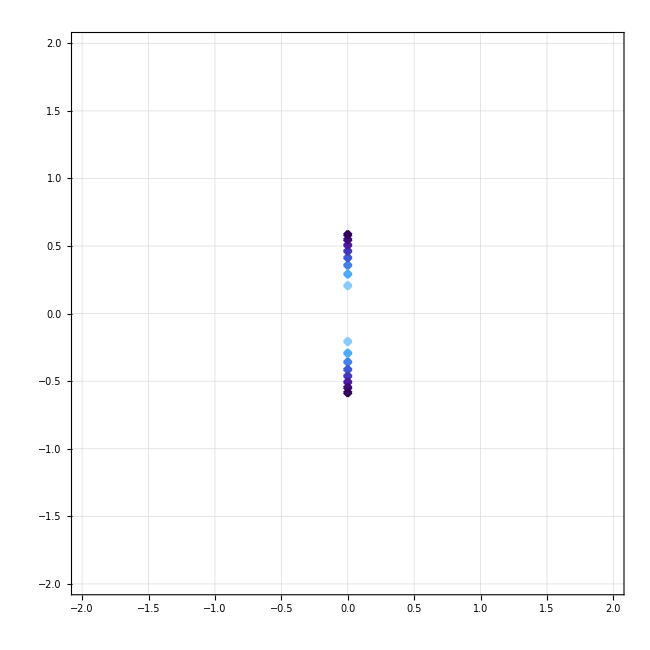

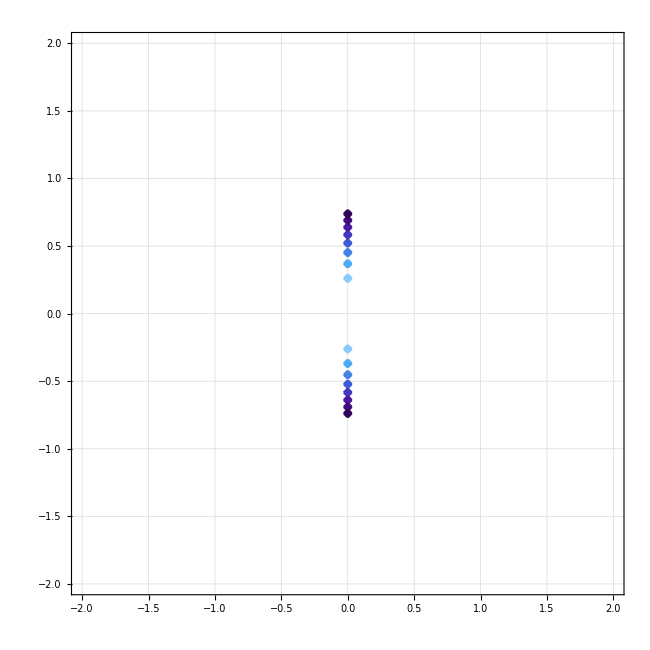

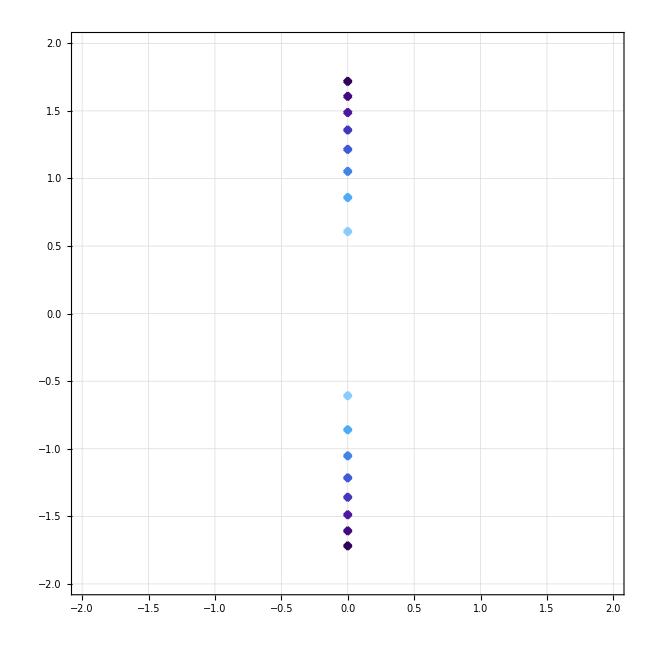

```mathematica
cross=Graphics[{Thickness[0.2],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]},ImagePadding->30];
kpoles1=Show[Array[ComplexListPlot[localsols3sign[0.04#,0.04#*0.7,0.04#*1.2,-2,-1,0.1,1][[1;;2]],PlotStyle->ColorData["DeepSeaColors"]/@{1-0.12*#},PlotMarkers->{cross,0.14},PlotRange->{{-2,2},{-2,2}}]&,8],Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Im}[k]",Magnification->3],FontSize->16],},{Style[MaTeX["\mathfrak{Re}[k]",Magnification->3],FontSize->16],}},AspectRatio->1,FrameTicksStyle->Directive[FontSize->24],ImageSize->650]
kpoles2=Show[Array[ComplexListPlot[localsols3sign[0.04#,0.04#*0.7,0.04#*1.2,-2,-1,0.1,1][[3;;4]],PlotStyle->ColorData["DeepSeaColors"]/@{1-0.12*#},PlotMarkers->{cross,0.14},PlotRange->{{-2,2},{-2,2}}]&,8],Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Im}[k]",Magnification->3],FontSize->16],},{Style[MaTeX["\mathfrak{Re}[k]",Magnification->3],FontSize->16],}},AspectRatio->1,FrameTicksStyle->Directive[FontSize->24],ImageSize->650]
kpoles3=Show[Array[ComplexListPlot[localsols3sign[0.04#,0.04#*0.7,0.04#*1.2,-2,-1,0.1,1][[5;;6]],PlotStyle->ColorData["DeepSeaColors"]/@{1-0.12*#},PlotMarkers->{cross,0.14},PlotRange->{{-2,2},{-2,2}}]&,8],Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Im}[k]",Magnification->3],FontSize->24],},{Style[MaTeX["\mathfrak{Re}[k]",Magnification->3],FontSize->24],}},AspectRatio->1,FrameTicksStyle->Directive[FontSize->24],ImageSize->650]
Export["/ssd/ri47hud/Projects/LG Analysis of cBC/figures/kpoles1.pdf",kpoles1];
Export["/ssd/ri47hud/Projects/LG Analysis of cBC/figures/kpoles2.pdf",kpoles2];
Export["/ssd/ri47hud/Projects/LG Analysis of cBC/figures/kpoles3.pdf",kpoles3];
```

### Non-local correlator: 3 zero modes

```mathematica
{np,n0,nm}={2,1,1};
χs3sign={{0,1,1},{1,0,0},{1,0,0}};
MatrixForm[χs3sign];
MatrixForm[G3sign[0,(ρ^2+1)/4,mup,mu0,mum,np,n0,nm,χs3sign,0,0,0,B1,B2,B3]];
MatrixForm[Inverse[G3sign[0,(ρ^2+1)/4,mup,mu0,mum,np,n0,nm,χs3sign,0,0,0,B1,B2,B3]]];
Collect[Simplify[Det[G3sign[0,(ρ^2+1)/4,mup,mu0,mum,np,n0,nm,χs3sign,0,0,0,B1,B2,B3]],mup<0&&mu0<0&&mum<0&&a>0],(1+ρ^2)];
Simplify[Denominator[Inverse[G3sign[0,(ρ^2+1)/4,mup,mu0,mum,np,n0,nm,χs3sign,0,0,0,B1,B2,B3]][[1,1]]]];
Simplify[MatrixForm[Inverse[G3sign[0,(ρ^2+1)/4,mup,mu0,mum,np,n0,nm,χs3sign,0,0,0,B1,B2,B3]]],ρ==I];
nonlocalsols[mup_,mu0_,mum_,B1_,B2_,B3_]:=ρ/.Simplify[Solve[Simplify[Det[G3sign[0,(ρ^2+1)/4,mup,mu0,mum,np,n0,nm,χs3sign,0,0,0,B1,B2,B3]],a>0]==0,ρ]]
```

```mathematica
nonlocalsols[1,1,2,-1,2,3]/.{a->1}
Manipulate[ComplexListPlot[nonlocalsols[mup,0.8mup,1.2mup,1,B1,B2,B3]/.{a->1},PlotRange->{{-2,2},{-2,2}},PlotStyle->{Red,PointSize[Large]}],{mup,-1,0},{B1,-2,2},{B2,-2,2},{B3,-2,2}]
```

{-ⅈ,ⅈ,-1/2 ⅈ √(4+1/3 (1+√37)),1/2 ⅈ √(4+1/3 (1+√37)),-1/2 ⅈ √(4+1/3 (1-√37)),1/2 ⅈ √(4+1/3 (1-√37))}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

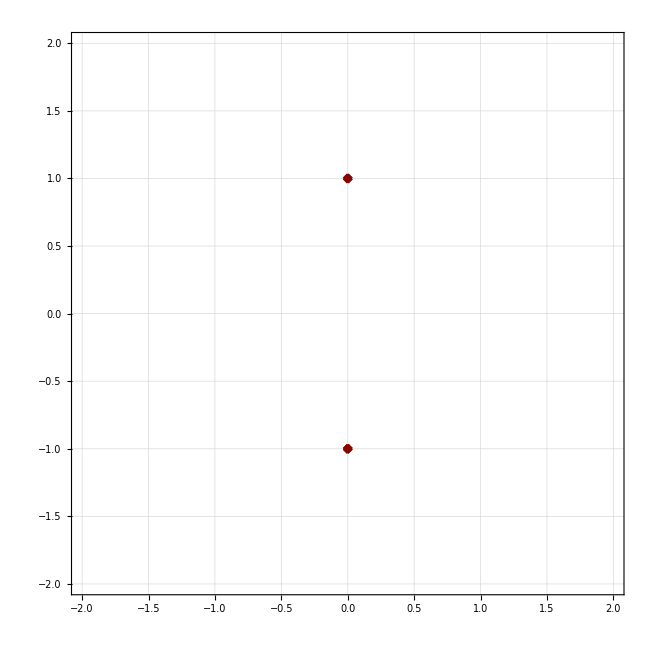

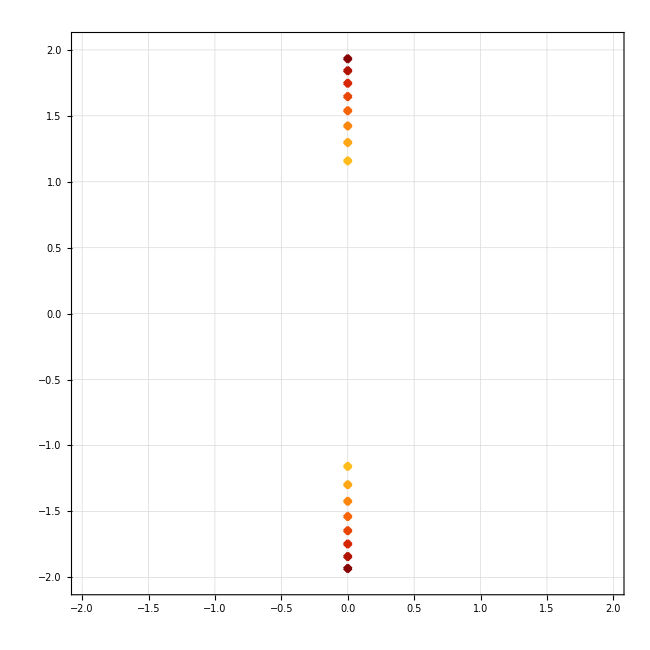

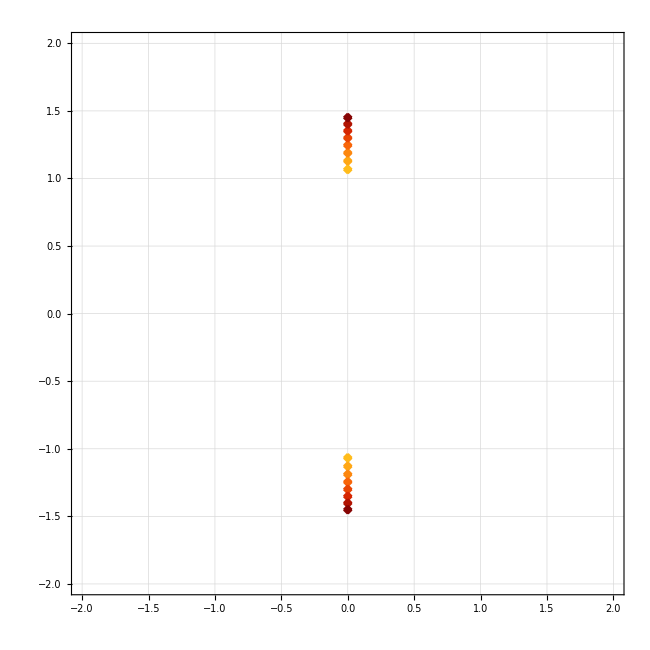

```mathematica
rhopoles1=Show[Array[ComplexListPlot[nonlocalsols[0.2#,0.2#*0.8,0.2#*1.2,1,1,1,2][[1;;2]],PlotStyle->ColorData["SolarColors"]/@{1-0.12*#},PlotMarkers->{cross,0.14},PlotRange->{{-2,2},{-2,2}}]&,8],Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Im}[{\varrho}]",Magnification->3],FontSize->16],},{Style[MaTeX["\mathfrak{Re}[\varrho]",Magnification->3],FontSize->16],}},AspectRatio->1,FrameTicksStyle->Directive[FontSize->24],ImageSize->650]
rhopoles2=Show[Array[ComplexListPlot[nonlocalsols[0.2#,0.2#*0.8,0.2#*1.2,1,1,1,2][[3;;4]],PlotStyle->ColorData["SolarColors"]/@{1-0.12*#},PlotMarkers->{cross,0.14},PlotRange->{{-2,2},{-2.05,2.05}}]&,8],Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Im}[{\varrho}]",Magnification->3],FontSize->16],},{Style[MaTeX["\mathfrak{Re}[\varrho]",Magnification->3],FontSize->16],}},AspectRatio->1,FrameTicksStyle->Directive[FontSize->24],ImageSize->650]
rhopoles3=Show[Array[ComplexListPlot[nonlocalsols[0.2#,0.2#*0.8,0.2#*1.2,1,1,1,2][[5;;6]],PlotStyle->ColorData["SolarColors"]/@{1-0.12*#},PlotMarkers->{cross,0.14},PlotRange->{{-2,2},{-2,2}}]&,8],Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Im}[{\varrho}]",Magnification->3],FontSize->16],},{Style[MaTeX["\mathfrak{Re}[\varrho]",Magnification->3],FontSize->16],}},AspectRatio->1,FrameTicksStyle->Directive[FontSize->24],ImageSize->650]
Export["/ssd/ri47hud/Projects/LG Analysis of cBC/figures/rhopoles1.pdf",rhopoles1];
Export["/ssd/ri47hud/Projects/LG Analysis of cBC/figures/rhopoles2.pdf",rhopoles2];
Export["/ssd/ri47hud/Projects/LG Analysis of cBC/figures/rhopoles3.pdf",rhopoles3];
```

```mathematica
{np,n0}={3,2};
χs2sign={{1,2},{2,0}};
Simplify[Det[G2sign[0,(ρ^2+1)/4,mup,mu0,np,n0,χs2sign]],mup<0&&mu0<0&&a>0]
nonlocalsols2signpre=Solve[Simplify[Det[G2sign[0,(ρ^2+1)/4,mup,mu0,np,n0,χs2sign]],mup<0&&mu0<0&&a>0]==0,ρ];
Array[Simplify[NumberForm[N[ρ/.nonlocalsols2signpre[[#]]]],mup<0&&mu0<0&&a>0]&,4]
nonlocalsols2sign[mup_,mu0_,a_]:={"0."-"1." ⅈ,"0."+"1." ⅈ,"-1." √("-1."+a^("2") ("-1." mu0-"1." mup)),√("-1."+a^("2") ("-1." mu0-"1." mup))}
Manipulate[ComplexListPlot[nonlocalsols2sign[mup,0.2mup,1],PlotRange->{{-3,3},{-3,3}},PlotStyle->{Red,PointSize[Large]}],{mup,0,10}]
```

((1+ρ^2) (a^2 (3 mu0+2 mup)+3 (1+ρ^2)))/(3 a^4)

{0.-1. ⅈ,0.+1. ⅈ,-0.57735 √(-3.+a^2 (-3. mu0-2. mup)),0.57735 √(-3.+a^2 (-3. mu0-2. mup))}

ComplexListPlot::ldata: nonlocalsols2sign[3.4,0.68,1] is not a valid dataset or list of datasets.

```mathematica
Clear[np,n0,nm]
chi={{1,0,1},{1,0,0},{0,1,0}};
Collect[Det[G3sign[0,(ρ^2+1)/4,mup,mu0,mum,2,1,1,chi]],(ρ^2+1)/a^2]
```

(mu0 mum mup)/2-1/2 √(mu0 mum) √(mu0 mup) √(mum mup)+((mu0 mum+(mu0 mup)/2+(mum mup)/2) (1+ρ^2))/a^2+((mu0+mum+mup/2) (1+ρ^2)^2)/a^4+((1+ρ^2)^3)/a^6

```mathematica
rhopoles1=Show[Array[ComplexListPlot[nonlocalsolsbelowthird[0.5#,0.5*0.4#,0.5*1.1#,1][[1;;2]],PlotStyle->ColorData["RustTones"]/@{1-0.12*#},PlotMarkers->{cross,0.14},PlotRange->{{-2.6,2.6},{-2.6,2.6}}]&,8],Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Im}[{\varrho}]",Magnification->3],FontSize->16],},{Style[MaTeX["\mathfrak{Re}[\varrho]",Magnification->3],FontSize->16],}},AspectRatio->1,FrameTicksStyle->Directive[FontSize->24],ImageSize->650];
rhopoles2=Show[Array[ComplexListPlot[nonlocalsolsbelowthird[0.5#,0.5*0.4#,0.5*1.1#,1][[3;;4]],PlotStyle->ColorData["RustTones"]/@{1-0.12*#},PlotMarkers->{cross,0.14},PlotRange->{{-2.6,2.6},{-2.6,2.6}}]&,8],Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Im}[{\varrho}]",Magnification->3],FontSize->16],},{Style[MaTeX["\mathfrak{Re}[\varrho]",Magnification->3],FontSize->16],}},AspectRatio->1,FrameTicksStyle->Directive[FontSize->24],ImageSize->650];
rhopoles3=Show[Array[ComplexListPlot[nonlocalsolsbelowthird[0.5#,0.5*0.4#,0.5*1.1#,1][[5;;6]],PlotStyle->ColorData["RustTones"]/@{1-0.12*#},PlotMarkers->{cross,0.14},PlotRange->{{-2.6,2.6},{-2.6,2.6}}]&,8],Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Im}[{\varrho}]",Magnification->3],FontSize->16],},{Style[MaTeX["\mathfrak{Re}[\varrho]",Magnification->3],FontSize->16],}},AspectRatio->1,FrameTicksStyle->Directive[FontSize->24],ImageSize->650];
(*Export["/ssd/ri47hud/Projects/LG Analysis of cBC/figures/rhopoles11.pdf",rhopoles11];
Export["/ssd/ri47hud/Projects/LG Analysis of cBC/figures/rhopoles21.pdf",rhopoles21];
Export["/ssd/ri47hud/Projects/LG Analysis of cBC/figures/rhopoles31.pdf",rhopoles31];*)
```

ComplexListPlot::ldata: nonlocalsolsbelowthird[0.5,0.2] is not a valid dataset or list of datasets.

ComplexListPlot::ldata: nonlocalsolsbelowthird[1.,0.4] is not a valid dataset or list of datasets.

ComplexListPlot::ldata: nonlocalsolsbelowthird[1.5,0.6] is not a valid dataset or list of datasets.

General::stop: Further output of ComplexListPlot::ldata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ComplexListPlot[nonlocalsolsbelowthird[0.5,0.2],PlotStyle→{color},PlotMarkers→{,0.14},PlotRange→{{-2.6,2.6},{-2.6,2.6}}],ComplexListPlot[nonlocalsolsbelowthird[1.,0.4],PlotStyle→{color},PlotMarkers→{,0.14},PlotRange→{{-2.6,2.6},{-2.6,2.6}}],«5»,ComplexListPlot[nonlocalsolsbelowthird[4.,1.6],PlotStyle→{color},PlotMarkers→{,0.14},PlotRange→{{-2.6,2.6},{-2.6,2.6}}]},Frame→True,GridLines→Automatic,«10»→«1»,AspectRatio→1,FrameTicksStyle→Directive[FontSize→24],ImageSize→650].

ComplexListPlot::ldata: nonlocalsolsbelowthird[0.55,1] is not a valid dataset or list of datasets.

ComplexListPlot::ldata: nonlocalsolsbelowthird[1.1,1] is not a valid dataset or list of datasets.

ComplexListPlot::ldata: nonlocalsolsbelowthird[1.65,1] is not a valid dataset or list of datasets.

General::stop: Further output of ComplexListPlot::ldata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ComplexListPlot[nonlocalsolsbelowthird[0.55,1],PlotStyle→{color},PlotMarkers→{,0.14},PlotRange→{{-2.6,2.6},{-2.6,2.6}}],ComplexListPlot[nonlocalsolsbelowthird[1.1,1],PlotStyle→{color},PlotMarkers→{,0.14},PlotRange→{{-2.6,2.6},{-2.6,2.6}}],«5»,ComplexListPlot[nonlocalsolsbelowthird[4.4,1],PlotStyle→{color},PlotMarkers→{,0.14},PlotRange→{{-2.6,2.6},{-2.6,2.6}}]},Frame→True,GridLines→Automatic,FrameLabel→«1»,AspectRatio→1,FrameTicksStyle→Directive[FontSize→24],ImageSize→650].

Part::take: Cannot take positions 5 through 6 in nonlocalsolsbelowthird[0.5,0.2,0.55,1].

Part::take: Cannot take positions 5 through 6 in nonlocalsolsbelowthird[0.5,0.2,0.55,1.].

General::stop: Further output of Part::take will be suppressed during this calculation.

ComplexListPlot::ldata: nonlocalsolsbelowthird[0.5,0.2,0.55,1]⟦5;;6⟧ is not a valid dataset or list of datasets.

ComplexListPlot::ldata: nonlocalsolsbelowthird[1.,0.4,1.1,1]⟦5;;6⟧ is not a valid dataset or list of datasets.

ComplexListPlot::ldata: nonlocalsolsbelowthird[1.5,0.6,1.65,1]⟦5;;6⟧ is not a valid dataset or list of datasets.

General::stop: Further output of ComplexListPlot::ldata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ComplexListPlot[nonlocalsolsbelowthird[0.5,0.2,0.55,1]⟦5;;6⟧,PlotStyle→{color},PlotMarkers→{,0.14},PlotRange→{{-2.6,2.6},{-2.6,2.6}}],ComplexListPlot[nonlocalsolsbelowthird[1.,0.4,1.1,1]⟦5;;6⟧,PlotStyle→{color},PlotMarkers→{,0.14},PlotRange→{{-2.6,2.6},{-2.6,2.6}}],«5»,ComplexListPlot[nonlocalsolsbelowthird[4.,1.6,4.4,1]⟦5;;6⟧,PlotStyle→{color},PlotMarkers→{,0.14},PlotRange→{{-2.6,2.6},{-2.6,2.6}}]},Frame→True,«3»,FrameTicksStyle→Directive[«1»],ImageSize→650].

### Non-local correlator: 2 zero modes

```mathematica
detG2[k_,ρ1_,ρ2_,mup_,mu0_,mum_,χ_]:=(((ρ2^2+1)+(ρ1^2+1))/a^2+A k^2+mum-mum χ) (-mu0 mup χ^2+(((ρ2^2+1)+(ρ1^2+1))/a^2+A k^2+mu0-mu0 χ) (((ρ2^2+1)+(ρ1^2+1))/a^2+A k^2+mup-mup χ))-(χ^2 (((ρ2^2+1)+(ρ1^2+1)) mu0 mum+a^2 (A k^2 mu0 mum-mu0 mum mup (-1+χ)+mu0 mum  mup  χ)))/a^2-(χ^2 (((ρ2^2+1)+(ρ1^2+1)) mum mup+a^2 (A k^2 mum mup-mu0 mum mup (-1+χ)+mu0 mum  mup χ)))/a^2;
```

```mathematica
Simplify[ReIm[N[3^(1/6) (5 (6 ⅈ √3+√17) (-18+ⅈ √51)^(1/3)-3^(1/6) (91 ⅈ+12 √51))a^2 mu]],a^2>0&&mu>0]
```

{-216.842 a^2 mu,23.0493 a^2 mu}

### O(3)-invariant theory

```mathematica
GO3[Np_,Nz_,Nm_,chi1_,chi2_,μ_,n_]:={{-Δ+μ(1-(Np^2*chi1+2chi2[[1]](Nz^2+Nm^2))/n),(2chi2[[2]]Np*Nz)/n,(2chi2[[2]]Np*Nm)/n},{(2chi2[[2]]Nz*Np)/n,-Δ+μ(1-(Nz^2*chi1+2chi2[[1]](Np^2+Nm^2))/n),(2chi2[[2]]Nz*Nm)/n},{(2chi2[[2]]Np*Nm)/n,(2chi2[[2]]Nz*Nm)/n,-Δ+μ(1-(Nm^2*chi1+2chi2[[1]](Np^2+Nz^2))/n)}}
```

```mathematica
chi1=4;
chi2={1,1};
MatrixForm[GO3[Np,Nz,Nm,chi1,chi2,μ,n]]
Simplify[Det[GO3[Np,Nz,Nm,chi1,chi2,μ,4]],Np^2+Nz^2+Nm^2==1&&μ<0]
MatrixForm[Simplify[Inverse[GO3[Np,Nz,Nm,chi1,chi2,μ,4]],Np^2+Nz^2+Nm^2==1&&μ<0]]
FullSimplify[Sum[(Inverse[GO3[Np,Nz,Nm,chi1,chi2,μ,4]][[i,i]])^2,{i,1,3}],Np^2+Nz^2+Nm^2==1&&μ<0]
```

(-Δ+(1-(4 Np^2+2 (Nm^2+Nz^2))/n) μ | (2 Np Nz)/n | (2 Nm Np)/n
(2 Np Nz)/n | -Δ+(1-(2 (Nm^2+Np^2)+4 Nz^2)/n) μ | (2 Nm Nz)/n
(2 Nm Np)/n | (2 Nm Nz)/n | -Δ+(1-(4 Nm^2+2 (Np^2+Nz^2))/n) μ)

1/8 (-2 Δ (-2 Δ+μ)^2-Nz^2 (2 Δ-μ) (-1+μ^2)+Nz^4 (2 Δ-μ) (-1+μ^2)+Np^4 (Nz^2 (-2+μ) (1+μ)^2+(2 Δ-μ) (-1+μ^2))+Np^2 (-1+Nz^2) (1+μ) ((2 Δ-μ) (-1+μ)+Nz^2 (-2-μ+μ^2)))

((-8 Δ^2+4 (1+Np^2) Δ μ-2 Np^2 μ^2+2 (-1+Np^2) Nz^2 (-1+μ^2)+2 Nz^4 (-1+μ^2))/(2 Δ (-2 Δ+μ)^2+Nz^2 (2 Δ-μ) (-1+μ^2)-Nz^4 (2 Δ-μ) (-1+μ^2)-Np^2 (-1+Nz^2) (1+μ) ((2 Δ-μ) (-1+μ)+Nz^2 (-2-μ+μ^2))+Np^4 (-((2 Δ-μ) (-1+μ^2))+Nz^2 (2+3 μ-μ^3))) | -(2 Np Nz (-1-2 Δ+Np^2 (1+μ)+Nz^2 (1+μ)))/(-2 Δ (-2 Δ+μ)^2-Nz^2 (2 Δ-μ) (-1+μ^2)+Nz^4 (2 Δ-μ) (-1+μ^2)+Np^4 (Nz^2 (-2+μ) (1+μ)^2+(2 Δ-μ) (-1+μ^2))+Np^2 (-1+Nz^2) (1+μ) ((2 Δ-μ) (-1+μ)+Nz^2 (-2-μ+μ^2))) | (2 Nm Np (2 Δ-μ+Nz^2 (1+μ)))/(-2 Δ (-2 Δ+μ)^2-Nz^2 (2 Δ-μ) (-1+μ^2)+Nz^4 (2 Δ-μ) (-1+μ^2)+Np^4 (Nz^2 (-2+μ) (1+μ)^2+(2 Δ-μ) (-1+μ^2))+Np^2 (-1+Nz^2) (1+μ) ((2 Δ-μ) (-1+μ)+Nz^2 (-2-μ+μ^2)))
-(2 Np Nz (-1-2 Δ+Np^2 (1+μ)+Nz^2 (1+μ)))/(-2 Δ (-2 Δ+μ)^2-Nz^2 (2 Δ-μ) (-1+μ^2)+Nz^4 (2 Δ-μ) (-1+μ^2)+Np^4 (Nz^2 (-2+μ) (1+μ)^2+(2 Δ-μ) (-1+μ^2))+Np^2 (-1+Nz^2) (1+μ) ((2 Δ-μ) (-1+μ)+Nz^2 (-2-μ+μ^2))) | (-8 Δ^2+4 (1+Nz^2) Δ μ-2 Nz^2 μ^2+2 Np^4 (-1+μ^2)+2 Np^2 (-1+Nz^2) (-1+μ^2))/(2 Δ (-2 Δ+μ)^2+Nz^2 (2 Δ-μ) (-1+μ^2)-Nz^4 (2 Δ-μ) (-1+μ^2)-Np^2 (-1+Nz^2) (1+μ) ((2 Δ-μ) (-1+μ)+Nz^2 (-2-μ+μ^2))+Np^4 (-((2 Δ-μ) (-1+μ^2))+Nz^2 (2+3 μ-μ^3))) | (2 Nm Nz (2 Δ-μ+Np^2 (1+μ)))/(-2 Δ (-2 Δ+μ)^2-Nz^2 (2 Δ-μ) (-1+μ^2)+Nz^4 (2 Δ-μ) (-1+μ^2)+Np^4 (Nz^2 (-2+μ) (1+μ)^2+(2 Δ-μ) (-1+μ^2))+Np^2 (-1+Nz^2) (1+μ) ((2 Δ-μ) (-1+μ)+Nz^2 (-2-μ+μ^2)))
(2 Nm Np (2 Δ-μ+Nz^2 (1+μ)))/(-2 Δ (-2 Δ+μ)^2-Nz^2 (2 Δ-μ) (-1+μ^2)+Nz^4 (2 Δ-μ) (-1+μ^2)+Np^4 (Nz^2 (-2+μ) (1+μ)^2+(2 Δ-μ) (-1+μ^2))+Np^2 (-1+Nz^2) (1+μ) ((2 Δ-μ) (-1+μ)+Nz^2 (-2-μ+μ^2))) | (2 Nm Nz (2 Δ-μ+Np^2 (1+μ)))/(-2 Δ (-2 Δ+μ)^2-Nz^2 (2 Δ-μ) (-1+μ^2)+Nz^4 (2 Δ-μ) (-1+μ^2)+Np^4 (Nz^2 (-2+μ) (1+μ)^2+(2 Δ-μ) (-1+μ^2))+Np^2 (-1+Nz^2) (1+μ) ((2 Δ-μ) (-1+μ)+Nz^2 (-2-μ+μ^2))) | (-8 Δ^2-4 (-2+Nz^2) Δ μ+2 (-1+Nz^2) μ^2+Np^2 (2 μ (-2 Δ+μ)+Nz^2 (2-2 μ^2)))/(2 Δ (-2 Δ+μ)^2+Nz^2 (2 Δ-μ) (-1+μ^2)-Nz^4 (2 Δ-μ) (-1+μ^2)-Np^2 (-1+Nz^2) (1+μ) ((2 Δ-μ) (-1+μ)+Nz^2 (-2-μ+μ^2))+Np^4 (-((2 Δ-μ) (-1+μ^2))+Nz^2 (2+3 μ-μ^3))))

(4 (Np^8 (-1+μ^2)^2-2 Nz^6 (-1+μ^2)^2+Nz^8 (-1+μ^2)^2+2 Np^6 (-1+Nz^2) (-1+μ^2)^2+(-2 Δ+μ)^2 (12 Δ^2-4 Δ μ+μ^2)-2 Nz^2 (2 Δ-μ) (2 Δ-μ^3)+Nz^4 (1+8 Δ^2-2 μ^2+3 μ^4-4 Δ (μ+μ^3))+Np^4 (1+8 Δ^2-2 μ^2+3 μ^4+2 Nz^2 (1+6 Δ μ-4 μ^2) (-1+μ^2)+3 Nz^4 (-1+μ^2)^2-4 Δ (μ+μ^3))+2 Np^2 (-1+Nz^2) (4 Δ^2+μ^4+3 Nz^2 (2 Δ-μ) μ (-1+μ^2)+Nz^4 (-1+μ^2)^2-2 Δ (μ+μ^3))))/(Np^2 (-1+Nz^2) (1+μ) ((2 Δ-μ) (-1+μ)+Nz^2 (-2+μ) (1+μ))+(2 Δ-μ) (2 Δ (-2 Δ+μ)+Nz^2 (-1+Nz^2) (-1+μ^2))+Np^4 (Nz^2 (-2+μ) (1+μ)^2+(2 Δ-μ) (-1+μ^2)))^2

```mathematica
Clear[n]
```

s_0<=s<r

```mathematica
chi1=4;
chi2={0,2};
Simplify[Det[GO3[1,0,0,chi1,chi2,μ,4]]]
MatrixForm[Simplify[Inverse[GO3[1,0,0,chi1,chi2,μ,4]],Np^2+Nz^2+Nm^2==1]]
FullSimplify[Sum[Inverse[GO3[1,0,0,chi1,chi2,μ,4]][[i,i]],{i,1,3}],Np^2+Nz^2+Nm^2==1]
```

-Δ (Δ-μ)^2

(-1/Δ | 0 | 0
0 | 1/(-Δ+μ) | 0
0 | 0 | 1/(-Δ+μ))

-1/Δ+2/(-Δ+μ)

s<s_0

```mathematica
chi1=0;
chi2={0,0};
Simplify[Det[GO3[1,0,0,chi1,chi2,μ,4]]]
MatrixForm[Simplify[Inverse[GO3[1,0,0,chi1,chi2,μ,4]],Np^2+Nz^2+Nm^2==1]]
FullSimplify[Sum[Inverse[GO3[1,0,0,chi1,chi2,μ,4]][[i,i]],{i,1,3}],Np^2+Nz^2+Nm^2==1]
```

-(Δ-μ)^3

(1/(-Δ+μ) | 0 | 0
0 | 1/(-Δ+μ) | 0
0 | 0 | 1/(-Δ+μ))

3/(-Δ+μ)

s = r

```mathematica
MatrixForm[GO3[1,0,0,12,{2,4},μ,4]]
Simplify[Det[GO3[1,0,0,12,{2,4},μ,4]],Np^2+Nz^2+Nm^2==1&&μ<0]
MatrixForm[Simplify[Inverse[GO3[1,0,0,12,{2,4},μ,4]],Np^2+Nz^2+Nm^2==1&&μ<0]]
FullSimplify[Sum[Inverse[GO3[1,0,0,12,{2,4},μ,4]][[i,i]],{i,1,3}],Np^2+Nz^2+Nm^2==1&&μ<0]
```

(-Δ-2 μ | 0 | 0
0 | -Δ | 0
0 | 0 | -Δ)

-Δ^2 (Δ+2 μ)

(-1/(Δ+2 μ) | 0 | 0
0 | -1/Δ | 0
0 | 0 | -1/Δ)

-2/Δ-1/(Δ+2 μ)

### CDT-like interactions

```mathematica
CDTmfsols=Simplify[Solve[mup*phip+λ1*phim^4*vol^10==0&&mum*phim+4λ1*phip*phim^3*vol^10+5λ2*phim^4*vol^10==0,{phip,phim}],mup<0&&mum<0&&vol>0&&λ1>0&&λ2>0];
{phip,phim}/.CDTmfsols[[3]]
Array[(({phip,phim}/.CDTmfsols[[#]])[[2]])^3&,6]
```

{((-1)^(1/3) (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))^(4/3))/(16 mup vol^(10/3) λ1^(5/3)),-1/2 (-1)^(1/3) ((5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))/(vol^10 λ1^2))^(1/3)}

{0,(5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))/(8 vol^10 λ1^2),(5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))/(8 vol^10 λ1^2),(5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))/(8 vol^10 λ1^2),(5 mup λ2-√(mup (16 mum λ1^2+25 mup λ2^2)))/(8 vol^10 λ1^2),(5 mup λ2-√(mup (16 mum λ1^2+25 mup λ2^2)))/(8 vol^10 λ1^2)}

```mathematica
HessianH[f_,x_List?VectorQ]:=D[f,{x,2}]
f[phip_,phim_]:=1/2 mup*phip^2+1/2 mum*phim^2+λ1*phip*phim^4*vol^10+λ2*phim^5*vol^10
```

```mathematica
HessianH[f[phip,phim],{phip,phim}]//MatrixForm
```

(mup | 4 phim^3 vol^10 λ1
4 phim^3 vol^10 λ1 | mum+12 phim^2 phip vol^10 λ1+20 phim^3 vol^10 λ2)

```mathematica
Simplify[Eigenvalues[{{mup,4 phim^3 vol^10 λ1},{4 phim^3 vol^10 λ1,mum+12 phim^2 phip vol^10 λ1+20 phim^3 vol^10 λ2}}],phip==0&&phim==0]
```

{1/2 (mum-√((mum-mup)^2)+mup),1/2 (mum+√((mum-mup)^2)+mup)}

```mathematica
phim^2*phip/.CDTmfsols[[2]]
```

-((5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))^(4/3) ((5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))/(vol^10 λ1^2))^(2/3))/(64 mup vol^(10/3) λ1^(5/3))

Local correlation function

```mathematica
CDTGloc[k_,mup_,mum_,A1_,A2_,λ1_,λ2_]:={{A1*k^2+mup,4λ1*phim^3},{4*λ1*phim^3,A2*k^2+mum+λ1*phip*phim^2*12+λ2*phim^3*20}}/.CDTmfsols[[2]]
```

```mathematica
CDTlocalsols[mup_,mum_,A1_,A2_,λ1_,λ2_]:=k/.Simplify[Solve[□Simplify[Det[CDTGloc[k,mup,mum,A1,A2,λ1,λ2]],vol==1]==0,k],Element[{λ1,λ2,A1,A2},Reals]]
```

```mathematica
CDTlocalsols[mup,mum,1,2,1,2];
```

```mathematica
Manipulate[ComplexListPlot[CDTlocalsols[mup,0.5mup,A1,A2,λ1,λ2],PlotRange->{{-3,3},{-3,3}},PlotStyle->{Red,PointSize[Large]}],{mup,-0.1,1},{A1,-2,2},{A2,-2,2},{λ1,-2,2},{λ2,-2,2}]
```

Non-local correlation function

```mathematica
CDTGnloc[ρ_,mup_,mum_,B1_,B2_,χ41pm_,χ41mm_,χ32_]:={{B1*(ρ^2+1)+mup,χ41pm*λ1*phim^3},{χ41pm*λ1*phim^3,B2*(ρ^2+1)+mum+λ1*phip*phim^2*χ41mm+λ2*phim^3*χ32}}/.CDTmfsols[[2]]
χ41pm=1;
χ41mm=3;
χ32=5;
CDTGnloc[ρ,mup,mum,B1,B2,χ41pm,χ41mm,χ32]//MatrixForm
Simplify[Inverse[CDTGnloc[ρ,mup,mum,B1,B2,χ41pm,χ41mm,χ32]],ρ>0&&mup<0&&mum<0&&vol==1]//MatrixForm
CDTnlocsols[mup_,mum_,B1_,B2_,λ1_,λ2_]:=ρ/.Solve[Simplify[Det[CDTGnloc[ρ,mup,mum,B1,B2,χ41pm,χ41mm,χ32]],ρ>0&&mup<0&&mum<0&&vol==1]==0,ρ]
```

(mup+B1 (1+ρ^2) | (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))/(8 vol^10 λ1)
(5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))/(8 vol^10 λ1) | mum+(5 λ2 (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2))))/(8 vol^10 λ1^2)-(3 (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))^(4/3) ((5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))/(vol^10 λ1^2))^(2/3))/(64 mup vol^(10/3) λ1^(2/3))+B2 (1+ρ^2))

((200 mup^2 λ2^2+40 mup λ2 √(mup (16 mum λ1^2+25 mup λ2^2))-3 λ1^(4/3) (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))^(4/3) ((5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))/λ1^2)^(2/3)+64 mup λ1^2 (B2+mum+B2 ρ^2))/(-16 mum mup^2 λ1^2-50 mup^3 λ2^2-10 mup^2 λ2 √(mup (16 mum λ1^2+25 mup λ2^2))+40 mup λ2 (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2))) (B1+mup+B1 ρ^2)-3 λ1^(4/3) (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))^(4/3) ((5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))/λ1^2)^(2/3) (B1+mup+B1 ρ^2)+64 mup λ1^2 (B1+mup+B1 ρ^2) (B2+mum+B2 ρ^2)) | -(8 mup λ1 (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2))))/(-16 mum mup^2 λ1^2-50 mup^3 λ2^2-10 mup^2 λ2 √(mup (16 mum λ1^2+25 mup λ2^2))+40 mup λ2 (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2))) (B1+mup+B1 ρ^2)-3 λ1^(4/3) (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))^(4/3) ((5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))/λ1^2)^(2/3) (B1+mup+B1 ρ^2)+64 mup λ1^2 (B1+mup+B1 ρ^2) (B2+mum+B2 ρ^2))
-(8 mup λ1 (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2))))/(-16 mum mup^2 λ1^2-50 mup^3 λ2^2-10 mup^2 λ2 √(mup (16 mum λ1^2+25 mup λ2^2))+40 mup λ2 (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2))) (B1+mup+B1 ρ^2)-3 λ1^(4/3) (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))^(4/3) ((5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))/λ1^2)^(2/3) (B1+mup+B1 ρ^2)+64 mup λ1^2 (B1+mup+B1 ρ^2) (B2+mum+B2 ρ^2)) | (64 λ1^2 (B1+mup+B1 ρ^2))/(-(5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))^2+((B1+mup+B1 ρ^2) (200 mup^2 λ2^2+40 mup λ2 √(mup (16 mum λ1^2+25 mup λ2^2))-3 λ1^(4/3) (5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))^(4/3) ((5 mup λ2+√(mup (16 mum λ1^2+25 mup λ2^2)))/λ1^2)^(2/3)+64 mup λ1^2 (B2+mum+B2 ρ^2)))/mup))

```mathematica
Manipulate[ComplexListPlot[CDTnlocsols[mup,0.5mup,B1,B2,λ1,λ2],PlotRange->{{-3,3},{-3,3}},PlotStyle->{Red,PointSize[Large]}],{mup,0.1,10},{B1,-10,10},{B2,-10,10},{λ1,-10,10},{λ2,-10,10}]
```

Simplify::fas: Warning: one or more assumptions evaluated to False.

### Colored simplicial GFT

```mathematica
coloredmfsols=Solve[μ*ϕ1+4λ*V^10 ϕ2*ϕ3*ϕ4*ϕ5==0&&μ*ϕ2+4λ*V^10 ϕ1*ϕ3*ϕ4*ϕ5==0&&μ*ϕ3+4λ*V^10 ϕ1*ϕ2*ϕ4*ϕ5==0&&μ*ϕ4+4λ*V^10 ϕ1*ϕ2*ϕ3*ϕ5==0&&μ*ϕ5+4λ*V^10 ϕ1*ϕ2*ϕ3*ϕ4==0,{ϕ1,ϕ2,ϕ3,ϕ4,ϕ5}];
```

```mathematica
Table[ϕ1*ϕ2*ϕ3/.coloredmfsols[[i]],{i,1,Length[coloredmfsols]}];
```

```mathematica
Table[{ϕ3*ϕ4*ϕ5/.coloredmfsols[[i]],ϕ2*ϕ4*ϕ5/.coloredmfsols[[i]],ϕ2*ϕ3*ϕ5/.coloredmfsols[[i]],ϕ2*ϕ3*ϕ4/.coloredmfsols[[i]]},{i,1,Length[coloredmfsols]}];
```

```mathematica
Gloc[μ_,k_,B_,ϵ_]:={{B*k^2+μ,0,0,0,0},{0,B*k^2+μ,0,0,0},{0,0,B*k^2+μ,0,0},{0,0,0,B*k^2+μ,0},{0,0,0,0,B*k^2+μ}}+μ/4{{0,ϵ[[1]],ϵ[[2]],ϵ[[3]],ϵ[[4]]},{ϵ[[5]],0,ϵ[[6]],ϵ[[7]],ϵ[[8]]},{ϵ[[9]],ϵ[[10]],0,ϵ[[11]],ϵ[[12]]},{ϵ[[13]],ϵ[[14]],ϵ[[15]],0,ϵ[[16]]},{ϵ[[17]],ϵ[[18]],ϵ[[19]],ϵ[[20]],0}};
Simplify[MatrixForm[Inverse[Gloc[μ,k,A,Table[1,{i,1,20}]]]],k>0]
locsol[B_,μ_,ϵ_]:=k/.Simplify[Solve[Det[Gloc[μ,k,B,ϵ]]==0,k]]
locsol[A,μ,Table[1,{i,1,20}]]
Manipulate[ComplexListPlot[locsol[A,μ,Table[1,{i,1,20}]],PlotRange->{{-2,2},{-2,2}}],{A,-4,4},{μ,-2,0}]
```

((4 A k^2+7 μ)/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2)
-μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | (4 A k^2+7 μ)/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2)
-μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | (4 A k^2+7 μ)/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2)
-μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | (4 A k^2+7 μ)/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2)
-μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | -μ/(4 A^2 k^4+11 A k^2 μ+6 μ^2) | (4 A k^2+7 μ)/(4 A^2 k^4+11 A k^2 μ+6 μ^2))

{-(ⅈ √2 √μ)/(√A),(ⅈ √2 √μ)/(√A),-(ⅈ √3 √μ)/(2 √A),-(ⅈ √3 √μ)/(2 √A),-(ⅈ √3 √μ)/(2 √A),-(ⅈ √3 √μ)/(2 √A),(ⅈ √3 √μ)/(2 √A),(ⅈ √3 √μ)/(2 √A),(ⅈ √3 √μ)/(2 √A),(ⅈ √3 √μ)/(2 √A)}

```mathematica
χ3s[ϵ_]:=1/4{{0,ϵ[[1]],0,0,0},{0,0,ϵ[[2]],0,0},{0,0,0,ϵ[[3]],0},{0,0,0,0,ϵ[[4]]},{ϵ[[5]],0,0,0,0}};
G3snloc[μ_,ρ_,A_,ϵ_]:={{A*(ρ^2+1)+μ,0,0,0,0},{0,A*(ρ^2+1)+μ,0,0,0},{0,0,A*(ρ^2+1)+μ,0,0},{0,0,0,A*(ρ^2+1)+μ,0},{0,0,0,0,A*(ρ^2+1)+μ}}+μ*χ3s[ϵ];
Simplify[MatrixForm[Inverse[G3snloc[μ,ρ,1,{1,1,1,1,1}]]],ρ>0&&μ<0]
```

(((1+μ+ρ^2)^4)/(μ^5/1024+(1+μ+ρ^2)^5) | -(μ (1+μ+ρ^2)^3)/(4 (μ^5/1024+(1+μ+ρ^2)^5)) | (μ^2 (1+μ+ρ^2)^2)/(16 (μ^5/1024+(1+μ+ρ^2)^5)) | -(μ^3 (1+μ+ρ^2))/(64 (μ^5/1024+(1+μ+ρ^2)^5)) | μ^4/(256 (μ^5/1024+(1+μ+ρ^2)^5))
μ^4/(256 (μ^5/1024+(1+μ+ρ^2)^5)) | ((1+μ+ρ^2)^4)/(μ^5/1024+(1+μ+ρ^2)^5) | -(μ (1+μ+ρ^2)^3)/(4 (μ^5/1024+(1+μ+ρ^2)^5)) | (μ^2 (1+μ+ρ^2)^2)/(16 (μ^5/1024+(1+μ+ρ^2)^5)) | -(μ^3 (1+μ+ρ^2))/(64 (μ^5/1024+(1+μ+ρ^2)^5))
-(μ^3 (1+μ+ρ^2))/(64 (μ^5/1024+(1+μ+ρ^2)^5)) | μ^4/(256 (μ^5/1024+(1+μ+ρ^2)^5)) | ((1+μ+ρ^2)^4)/(μ^5/1024+(1+μ+ρ^2)^5) | -(μ (1+μ+ρ^2)^3)/(4 (μ^5/1024+(1+μ+ρ^2)^5)) | (μ^2 (1+μ+ρ^2)^2)/(16 (μ^5/1024+(1+μ+ρ^2)^5))
(μ^2 (1+μ+ρ^2)^2)/(16 (μ^5/1024+(1+μ+ρ^2)^5)) | -(μ^3 (1+μ+ρ^2))/(64 (μ^5/1024+(1+μ+ρ^2)^5)) | μ^4/(256 (μ^5/1024+(1+μ+ρ^2)^5)) | ((1+μ+ρ^2)^4)/(μ^5/1024+(1+μ+ρ^2)^5) | -(μ (1+μ+ρ^2)^3)/(4 (μ^5/1024+(1+μ+ρ^2)^5))
-(μ (1+μ+ρ^2)^3)/(4 (μ^5/1024+(1+μ+ρ^2)^5)) | (μ^2 (1+μ+ρ^2)^2)/(16 (μ^5/1024+(1+μ+ρ^2)^5)) | -(μ^3 (1+μ+ρ^2))/(64 (μ^5/1024+(1+μ+ρ^2)^5)) | μ^4/(256 (μ^5/1024+(1+μ+ρ^2)^5)) | ((1+μ+ρ^2)^4)/(μ^5/1024+(1+μ+ρ^2)^5))

```mathematica
Simplify[Solve[Det[G3snloc[μ,ρ,A,{1,1,1,1,1}]]==0,ρ],μ<0]
```

{{ρ→-(√(-4 A-3 μ))/(2 √A)},{ρ→(√(-4 A-3 μ))/(2 √A)},{ρ→-1/4 √(-16+((-17+√5+√(2 (5+√5)) √(-1/A^2) A) μ)/A)},{ρ→1/4 √(-16+((-17+√5+√(2 (5+√5)) √(-1/A^2) A) μ)/A)},{ρ→-1/4 √(-16+((-17+√5-√(2 (5+√5)) √(-1/A^2) A) μ)/A)},{ρ→1/4 √(-16+((-17+√5-√(2 (5+√5)) √(-1/A^2) A) μ)/A)},{ρ→-1/4 √(-16+√2 √((-5+√5)/A^2) μ-((17+√5) μ)/A)},{ρ→1/4 √(-16+√2 √((-5+√5)/A^2) μ-((17+√5) μ)/A)},{ρ→-1/4 √(-16-((17+√5) μ)/A+√2 √(((-5+√5) μ^2)/A^2))},{ρ→1/4 √(-16-((17+√5) μ)/A+√2 √(((-5+√5) μ^2)/A^2))}}

```mathematica
nlocsol[A_,μ_,ϵ_]:=ρ/.Simplify[Solve[Det[G3snloc[μ,ρ,A,ϵ]]==0,ρ]]
```

```mathematica
nlocsol[1,μ,{1,1,1,1,1}]
```

{-1/2 √(-4-3 μ),1/2 √(-4-3 μ),-1/4 √(-16+(-17+√5+ⅈ √(2 (5+√5))) μ),1/4 √(-16+(-17+√5+ⅈ √(2 (5+√5))) μ),-1/4 √(-16+(-17+√5-ⅈ √(2 (5+√5))) μ),1/4 √(-16+(-17+√5-ⅈ √(2 (5+√5))) μ),-1/4 √(-16-(17+√5-ⅈ √(10-2 √5)) μ),1/4 √(-16-(17+√5-ⅈ √(10-2 √5)) μ),-1/4 √(-16-(17+√5+ⅈ √(10-2 √5)) μ),1/4 √(-16-(17+√5+ⅈ √(10-2 √5)) μ)}

```mathematica
Manipulate[ComplexListPlot[nlocsol[A,μ,{1,-1,-1,-1,-1}],PlotRange->{{-2,2},{-2,2}}],{A,-2,2},{μ,-2,2}]
```

### Local theory in flat space and on the hyperboloid: 2 fields

```mathematica
Simplify[Solve[Subscript[μ, 1]+Subscript[n, 1]*λ*Subscript[ϕ, 1]^(Subscript[n, 1]-2)Subscript[ϕ, 2]^Subscript[n, 2]==0&&Subscript[μ, 2]+Subscript[n, 2]*λ*Subscript[ϕ, 1]^Subscript[n, 1] Subscript[ϕ, 2]^(Subscript[n, 2]-2)==0,{Subscript[ϕ, 1],Subscript[ϕ, 2]}],Element[{Subscript[μ, 1],Subscript[μ, 2],λ},Reals]]
```

{{ϕ_1→ⅇ^((2 (ⅈ π-Log[λ]-Log[n_1]+Log[μ_1])+(Log[n_1]-Log[n_2]-Log[μ_1]+Log[μ_2]) n_2)/(2 (-2+n_1+n_2))),ϕ_2→ⅇ^((2 (ⅈ π-Log[λ]-Log[n_2]+Log[μ_2])+(-Log[n_1]+Log[n_2]+Log[μ_1]-Log[μ_2]) n_1)/(2 (-2+n_1+n_2)))}}

```mathematica
Subscript[ϕ̄, 1]=ⅇ^((2 (ⅈ π-Log[λ]-Log[Subscript[n, 1]]+Log[Subscript[μ, 1]])+(Log[Subscript[n, 1]]-Log[Subscript[n, 2]]-Log[Subscript[μ, 1]]+Log[Subscript[μ, 2]]) Subscript[n, 2])/(2 (-2+Subscript[n, 1]+Subscript[n, 2])));
Subscript[ϕ̄, 2]=ⅇ^((2 (ⅈ π-Log[λ]-Log[Subscript[n, 2]]+Log[Subscript[μ, 2]])+(-Log[Subscript[n, 1]]+Log[Subscript[n, 2]]+Log[Subscript[μ, 1]]-Log[Subscript[μ, 2]]) Subscript[n, 1])/(2 (-2+Subscript[n, 1]+Subscript[n, 2])));
Subscript[f, 11]=Simplify[PowerExpand[λ*Subscript[n, 1]*(Subscript[n, 1]-1)Subscript[ϕ̄, 1]^(Subscript[n, 1]-2)Subscript[ϕ̄, 2]^Subscript[n, 2]],λ>0];
Subscript[f, 12]=Simplify[PowerExpand[λ*Subscript[n, 1]*Subscript[n, 2] Subscript[ϕ̄, 1]^(Subscript[n, 1]-1)Subscript[ϕ̄, 2]^(Subscript[n, 2]-1)],λ>0];
Subscript[f, 22]=Simplify[PowerExpand[λ*Subscript[n, 2]*(Subscript[n, 2]-1)Subscript[ϕ̄, 1]^Subscript[n, 1] Subscript[ϕ̄, 2]^(Subscript[n, 2]-2)],λ>0];
Glocflat2[k_,μ1_,μ2_,n1_,n2_]:={{k^2-μ1(n1-2),-Sqrt[n1*n2*μ1*μ2]},{-Sqrt[n1*n2*μ1*μ2],k^2-μ2(n2-2)}}
glocsolsflat2=Solve[Simplify[Det[Glocflat2[(q/r),m1,m2,7,2]],m1<0&&m2<0]==0,q];
Array[Simplify[NumberForm[N[q/.glocsolsflat2[[#]]]],m1<0&&m2<0]&,4]
```

{-0.707107 √((5. m1+1. √(m1 (25. m1+56. m2))) r^2),0.707107 √((5. m1+1. √(m1 (25. m1+56. m2))) r^2),-0.707107 √(5. m1 r^2+√m1 √(25. m1+56. m2) r^2),0.707107 √(5. m1 r^2+√m1 √(25. m1+56. m2) r^2)}

```mathematica
{{q->0},{q->0},{q->-√(-n r^2 μ1-4 r^2 μ2+n r^2 μ2)},{q->√(-n r^2 μ1-4 r^2 μ2+n r^2 μ2)}}
Integrate[(x^2 Sqrt[a*b]BesselJ[1,x])/(x^2(x^2+a+b)),{x,0,Infinity}]
```

{{q→0},{q→0},{q→-√(-n r^2 μ1-4 r^2 μ2+n r^2 μ2)},{q→√(-n r^2 μ1-4 r^2 μ2+n r^2 μ2)}}

ConditionalExpression[√(a b) (1/(a+b)-BesselK[1,√(a+b)]/(√(a+b))), Im[a]+Im[b]≠0||Re[a+b]≥0]

```mathematica
Simplify[{{(k^2+(4-n) μ2)/(k^4+k^2 n μ1+4 k^2 μ2-k^2 n μ2),-(√((4-n) n μ1 μ2))/(k^4+k^2 n μ1+4 k^2 μ2-k^2 n μ2)},{-(√((4-n) n μ1 μ2))/(k^4+k^2 n μ1+4 k^2 μ2-k^2 n μ2),(k^2+n μ1)/(k^4+k^2 n μ1+4 k^2 μ2-k^2 n μ2)}},n>0&&μ1<0&&μ2<0]
```

{{(k^2-(-4+n) μ2)/(k^2 (k^2+n (μ1-μ2)+4 μ2)),-(√(-((-4+n) n μ1 μ2)))/(k^2 (k^2+n (μ1-μ2)+4 μ2))},{-(√(-((-4+n) n μ1 μ2)))/(k^2 (k^2+n (μ1-μ2)+4 μ2)),(k^2+n μ1)/(k^2 (k^2+n (μ1-μ2)+4 μ2))}}

### Local theory in flat space and on the hyperboloid: 3 fields

```mathematica
Simplify[Solve[Subscript[μ, 1]+Subscript[n, 1]*λ*Subscript[ϕ, 1]^(Subscript[n, 1]-2)Subscript[ϕ, 2]^Subscript[n, 2] Subscript[ϕ, 3]^Subscript[n, 3]==0&&Subscript[μ, 2]+Subscript[n, 2]*λ*Subscript[ϕ, 1]^Subscript[n, 1] Subscript[ϕ, 2]^(Subscript[n, 2]-2)Subscript[ϕ, 3]^Subscript[n, 3]==0&&Subscript[μ, 3]+Subscript[n, 3]*λ*Subscript[ϕ, 1]^Subscript[n, 1] Subscript[ϕ, 2]^Subscript[n, 2] Subscript[ϕ, 3]^(Subscript[n, 3]-2)==0,{Subscript[ϕ, 1],Subscript[ϕ, 2],Subscript[ϕ, 3]}],Element[{Subscript[μ, 1],Subscript[μ, 2],Subscript[μ, 3],λ},Reals]];
Subscript[ϕ̄, 1]=ⅇ^((2 (ⅈ π-Log[λ]-Log[Subscript[n, 1]]+Log[Subscript[μ, 1]])+(Log[Subscript[n, 1]]-Log[Subscript[n, 2]]-Log[Subscript[μ, 1]]+Log[Subscript[μ, 2]]) Subscript[n, 2]+(Log[Subscript[n, 1]]-Log[Subscript[n, 3]]-Log[Subscript[μ, 1]]+Log[Subscript[μ, 3]]) Subscript[n, 3])/(2 (-2+Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3])));
Subscript[ϕ̄, 2]=ⅇ^((2 (ⅈ π-Log[λ]-Log[Subscript[n, 2]]+Log[Subscript[μ, 2]])+(-Log[Subscript[n, 1]]+Log[Subscript[n, 2]]+Log[Subscript[μ, 1]]-Log[Subscript[μ, 2]]) Subscript[n, 1]+(Log[Subscript[n, 2]]-Log[Subscript[n, 3]]-Log[Subscript[μ, 2]]+Log[Subscript[μ, 3]]) Subscript[n, 3])/(2 (-2+Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3])));
Subscript[ϕ̄, 3]=ⅇ^((2 (ⅈ π-Log[λ]-Log[Subscript[n, 3]]+Log[Subscript[μ, 3]])+(-Log[Subscript[n, 1]]+Log[Subscript[n, 3]]+Log[Subscript[μ, 1]]-Log[Subscript[μ, 3]]) Subscript[n, 1]+(-Log[Subscript[n, 2]]+Log[Subscript[n, 3]]+Log[Subscript[μ, 2]]-Log[Subscript[μ, 3]]) Subscript[n, 2])/(2 (-2+Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3])));
Subscript[f, 11]=Simplify[PowerExpand[λ*Subscript[n, 1]*(Subscript[n, 1]-1)Subscript[ϕ̄, 1]^(Subscript[n, 1]-2)Subscript[ϕ̄, 2]^Subscript[n, 2] Subscript[ϕ̄, 3]^Subscript[n, 3]],λ>0];
Subscript[f, 12]=Simplify[PowerExpand[λ*Subscript[n, 1]*Subscript[n, 2] Subscript[ϕ̄, 1]^(Subscript[n, 1]-1)Subscript[ϕ̄, 2]^(Subscript[n, 2]-1)Subscript[ϕ̄, 3]^Subscript[n, 3]],λ>0];
Glocflat3[k_,μ1_,μ2_,μ3_,n1_,n2_,n3_,A1_,A2_,A3_]:={{A1*k^2+μ1(2-n1),-Sqrt[μ1*μ2*n1*n2],-Sqrt[μ1*μ3*n1*n3]},{-Sqrt[μ2*μ1*n2*n1],A2*k^2+μ2(2-n2),-Sqrt[μ2*μ3*n2*n3]},{-Sqrt[μ3*μ1*n3*n1],-Sqrt[μ3*μ2*n3*n2],A3*k^2+μ3(2-n3)}}
Simplify[Det[Glocflat3[k,m1,m2,m3,4,2,1]],m1<0&&m2<0&&m3<0&&n1>0&&n2>0&&n3>0];
glocsolsflat3=Solve[Simplify[Det[Glocflat3[(q/r),m1,m2,m3,2,2,1,A1,A2,A3]],m1<0&&m2<0&&m3<0]==0,q];
Array[Simplify[NumberForm[N[q/.glocsolsflat3[[#]]]],m1<0&&m2<0&&m3<0]&,6]
solsflat3[m1_,m2_,m3_,r_,A1_,A2_,A3_]:={"-0.514361" √(("19.0488" A1 A2 A3^("2") m1 m2 r^("4")+"9.52441" A1 A2^("2") A3 m1 m3 r^("4")+"9.52441" A1^("2") A2 A3 m2 m3 r^("4")+"1.5874" A1^("2") A2^("2") m3^("2") r^("4")-"1.25992" A1 A2 m3 r^("2") ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("2"/"3"))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3"))),"0.514361" √(("19.0488" A1 A2 A3^("2") m1 m2 r^("4")+"9.52441" A1 A2^("2") A3 m1 m3 r^("4")+"9.52441" A1^("2") A2 A3 m2 m3 r^("4")+"1.5874" A1^("2") A2^("2") m3^("2") r^("4")-"1.25992" A1 A2 m3 r^("2") ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("2"/"3"))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3"))),"-1." √(-((("0.132283"+"0.229122" ⅈ) (("-9.52441"-"16.4968" ⅈ) A1 A2 A3^("2") m1 m2 r^("4")-("4.7622"+"8.24838" ⅈ) A1 A2^("2") A3 m1 m3 r^("4")-("4.7622"+"8.24838" ⅈ) A1^("2") A2 A3 m2 m3 r^("4")-("0.793701"+"1.37473" ⅈ) A1^("2") A2^("2") m3^("2") r^("4")+("0.629961"-"1.09112" ⅈ) A1 A2 m3 r^("2") ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("2"/"3")))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")))),√(-((("0.132283"+"0.229122" ⅈ) (("-9.52441"-"16.4968" ⅈ) A1 A2 A3^("2") m1 m2 r^("4")-("4.7622"+"8.24838" ⅈ) A1 A2^("2") A3 m1 m3 r^("4")-("4.7622"+"8.24838" ⅈ) A1^("2") A2 A3 m2 m3 r^("4")-("0.793701"+"1.37473" ⅈ) A1^("2") A2^("2") m3^("2") r^("4")+("0.629961"-"1.09112" ⅈ) A1 A2 m3 r^("2") ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("2"/"3")))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")))),"-1." √(-((("0.132283"-"0.229122" ⅈ) (("-9.52441"+"16.4968" ⅈ) A1 A2 A3^("2") m1 m2 r^("4")-("4.7622"-"8.24838" ⅈ) A1 A2^("2") A3 m1 m3 r^("4")-("4.7622"-"8.24838" ⅈ) A1^("2") A2 A3 m2 m3 r^("4")-("0.793701"-"1.37473" ⅈ) A1^("2") A2^("2") m3^("2") r^("4")+("0.629961"+"1.09112" ⅈ) A1 A2 m3 r^("2") ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("2"/"3")))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")))),√(-((("0.132283"-"0.229122" ⅈ) (("-9.52441"+"16.4968" ⅈ) A1 A2 A3^("2") m1 m2 r^("4")-("4.7622"-"8.24838" ⅈ) A1 A2^("2") A3 m1 m3 r^("4")-("4.7622"-"8.24838" ⅈ) A1^("2") A2 A3 m2 m3 r^("4")-("0.793701"-"1.37473" ⅈ) A1^("2") A2^("2") m3^("2") r^("4")+("0.629961"+"1.09112" ⅈ) A1 A2 m3 r^("2") ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("2"/"3")))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3"))))}
Manipulate[ComplexListPlot[solsflat3[m,0.5m,1.1m,1,1,1,A3],PlotRange->{{-2,2},{-2,2}},PlotStyle->{Red,PointSize[Large]}],{m,0,1},{A3,-1,1}]
```

{-0.514361 √((19.0488 A1 A2 A3^2 m1 m2 r^4+9.52441 A1 A2^2 A3 m1 m3 r^4+9.52441 A1^2 A2 A3 m2 m3 r^4+1.5874 A1^2 A2^2 m3^2 r^4-1.25992 A1 A2 m3 r^2 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)+1. (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(2/3))/(A1 A2 A3 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3))),0.514361 √((19.0488 A1 A2 A3^2 m1 m2 r^4+9.52441 A1 A2^2 A3 m1 m3 r^4+9.52441 A1^2 A2 A3 m2 m3 r^4+1.5874 A1^2 A2^2 m3^2 r^4-1.25992 A1 A2 m3 r^2 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)+1. (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(2/3))/(A1 A2 A3 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3))),-1. √(-(((0.132283+0.229122 ⅈ) ((-9.52441-16.4968 ⅈ) A1 A2 A3^2 m1 m2 r^4-(4.7622+8.24838 ⅈ) A1 A2^2 A3 m1 m3 r^4-(4.7622+8.24838 ⅈ) A1^2 A2 A3 m2 m3 r^4-(0.793701+1.37473 ⅈ) A1^2 A2^2 m3^2 r^4+(0.629961-1.09112 ⅈ) A1 A2 m3 r^2 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)+1. (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(2/3)))/(A1 A2 A3 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)))),√(-(((0.132283+0.229122 ⅈ) ((-9.52441-16.4968 ⅈ) A1 A2 A3^2 m1 m2 r^4-(4.7622+8.24838 ⅈ) A1 A2^2 A3 m1 m3 r^4-(4.7622+8.24838 ⅈ) A1^2 A2 A3 m2 m3 r^4-(0.793701+1.37473 ⅈ) A1^2 A2^2 m3^2 r^4+(0.629961-1.09112 ⅈ) A1 A2 m3 r^2 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)+1. (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(2/3)))/(A1 A2 A3 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)))),-1. √(-(((0.132283-0.229122 ⅈ) ((-9.52441+16.4968 ⅈ) A1 A2 A3^2 m1 m2 r^4-(4.7622-8.24838 ⅈ) A1 A2^2 A3 m1 m3 r^4-(4.7622-8.24838 ⅈ) A1^2 A2 A3 m2 m3 r^4-(0.793701-1.37473 ⅈ) A1^2 A2^2 m3^2 r^4+(0.629961+1.09112 ⅈ) A1 A2 m3 r^2 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)+1. (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(2/3)))/(A1 A2 A3 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)))),√(-(((0.132283-0.229122 ⅈ) ((-9.52441+16.4968 ⅈ) A1 A2 A3^2 m1 m2 r^4-(4.7622-8.24838 ⅈ) A1 A2^2 A3 m1 m3 r^4-(4.7622-8.24838 ⅈ) A1^2 A2 A3 m2 m3 r^4-(0.793701-1.37473 ⅈ) A1^2 A2^2 m3^2 r^4+(0.629961+1.09112 ⅈ) A1 A2 m3 r^2 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)+1. (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(2/3)))/(A1 A2 A3 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3))))}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ComplexListPlot::ldata: solsflat3[0.128,0.064,0.1408,1,1,1,-0.1] is not a valid dataset or list of datasets.

```mathematica
{"-0.514361" √(("19.0488" A1 A2 A3^("2") m1 m2 r^("4")+"9.52441" A1 A2^("2") A3 m1 m3 r^("4")+"9.52441" A1^("2") A2 A3 m2 m3 r^("4")+"1.5874" A1^("2") A2^("2") m3^("2") r^("4")-"1.25992" A1 A2 m3 r^("2") ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("2"/"3"))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3"))),"0.514361" √(("19.0488" A1 A2 A3^("2") m1 m2 r^("4")+"9.52441" A1 A2^("2") A3 m1 m3 r^("4")+"9.52441" A1^("2") A2 A3 m2 m3 r^("4")+"1.5874" A1^("2") A2^("2") m3^("2") r^("4")-"1.25992" A1 A2 m3 r^("2") ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("2"/"3"))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3"))),"-1." √(-((("0.132283"+"0.229122" ⅈ) (("-9.52441"-"16.4968" ⅈ) A1 A2 A3^("2") m1 m2 r^("4")-("4.7622"+"8.24838" ⅈ) A1 A2^("2") A3 m1 m3 r^("4")-("4.7622"+"8.24838" ⅈ) A1^("2") A2 A3 m2 m3 r^("4")-("0.793701"+"1.37473" ⅈ) A1^("2") A2^("2") m3^("2") r^("4")+("0.629961"-"1.09112" ⅈ) A1 A2 m3 r^("2") ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("2"/"3")))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")))),√(-((("0.132283"+"0.229122" ⅈ) (("-9.52441"-"16.4968" ⅈ) A1 A2 A3^("2") m1 m2 r^("4")-("4.7622"+"8.24838" ⅈ) A1 A2^("2") A3 m1 m3 r^("4")-("4.7622"+"8.24838" ⅈ) A1^("2") A2 A3 m2 m3 r^("4")-("0.793701"+"1.37473" ⅈ) A1^("2") A2^("2") m3^("2") r^("4")+("0.629961"-"1.09112" ⅈ) A1 A2 m3 r^("2") ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("2"/"3")))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")))),"-1." √(-((("0.132283"-"0.229122" ⅈ) (("-9.52441"+"16.4968" ⅈ) A1 A2 A3^("2") m1 m2 r^("4")-("4.7622"-"8.24838" ⅈ) A1 A2^("2") A3 m1 m3 r^("4")-("4.7622"-"8.24838" ⅈ) A1^("2") A2 A3 m2 m3 r^("4")-("0.793701"-"1.37473" ⅈ) A1^("2") A2^("2") m3^("2") r^("4")+("0.629961"+"1.09112" ⅈ) A1 A2 m3 r^("2") ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("2"/"3")))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")))),√(-((("0.132283"-"0.229122" ⅈ) (("-9.52441"+"16.4968" ⅈ) A1 A2 A3^("2") m1 m2 r^("4")-("4.7622"-"8.24838" ⅈ) A1 A2^("2") A3 m1 m3 r^("4")-("4.7622"-"8.24838" ⅈ) A1^("2") A2 A3 m2 m3 r^("4")-("0.793701"-"1.37473" ⅈ) A1^("2") A2^("2") m3^("2") r^("4")+("0.629961"+"1.09112" ⅈ) A1 A2 m3 r^("2") ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("2"/"3")))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3 r^("6")-"18." A1^("2") A2^("3") A3 m1 m3^("2") r^("6")-"18." A1^("3") A2^("2") A3 m2 m3^("2") r^("6")-"2." A1^("3") A2^("3") m3^("3") r^("6")+√(A1^("3") A2^("3") (A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2")+"4." ("-1." A1 A2 m3^("2")-"6." A3 ("2." A3 m1 m2+A2 m1 m3+A1 m2 m3))^("3")) r^("12")))^("1"/"3"))))}
```

{-0.514361 √((19.0488 A1 A2 A3^2 m1 m2 r^4+9.52441 A1 A2^2 A3 m1 m3 r^4+9.52441 A1^2 A2 A3 m2 m3 r^4+1.5874 A1^2 A2^2 m3^2 r^4-1.25992 A1 A2 m3 r^2 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)+1. (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(2/3))/(A1 A2 A3 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3))),0.514361 √((19.0488 A1 A2 A3^2 m1 m2 r^4+9.52441 A1 A2^2 A3 m1 m3 r^4+9.52441 A1^2 A2 A3 m2 m3 r^4+1.5874 A1^2 A2^2 m3^2 r^4-1.25992 A1 A2 m3 r^2 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)+1. (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(2/3))/(A1 A2 A3 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3))),-1. √(-(((0.132283+0.229122 ⅈ) ((-9.52441-16.4968 ⅈ) A1 A2 A3^2 m1 m2 r^4-(4.7622+8.24838 ⅈ) A1 A2^2 A3 m1 m3 r^4-(4.7622+8.24838 ⅈ) A1^2 A2 A3 m2 m3 r^4-(0.793701+1.37473 ⅈ) A1^2 A2^2 m3^2 r^4+(0.629961-1.09112 ⅈ) A1 A2 m3 r^2 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)+1. (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(2/3)))/(A1 A2 A3 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)))),√(-(((0.132283+0.229122 ⅈ) ((-9.52441-16.4968 ⅈ) A1 A2 A3^2 m1 m2 r^4-(4.7622+8.24838 ⅈ) A1 A2^2 A3 m1 m3 r^4-(4.7622+8.24838 ⅈ) A1^2 A2 A3 m2 m3 r^4-(0.793701+1.37473 ⅈ) A1^2 A2^2 m3^2 r^4+(0.629961-1.09112 ⅈ) A1 A2 m3 r^2 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)+1. (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(2/3)))/(A1 A2 A3 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)))),-1. √(-(((0.132283-0.229122 ⅈ) ((-9.52441+16.4968 ⅈ) A1 A2 A3^2 m1 m2 r^4-(4.7622-8.24838 ⅈ) A1 A2^2 A3 m1 m3 r^4-(4.7622-8.24838 ⅈ) A1^2 A2 A3 m2 m3 r^4-(0.793701-1.37473 ⅈ) A1^2 A2^2 m3^2 r^4+(0.629961+1.09112 ⅈ) A1 A2 m3 r^2 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)+1. (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(2/3)))/(A1 A2 A3 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)))),√(-(((0.132283-0.229122 ⅈ) ((-9.52441+16.4968 ⅈ) A1 A2 A3^2 m1 m2 r^4-(4.7622-8.24838 ⅈ) A1 A2^2 A3 m1 m3 r^4-(4.7622-8.24838 ⅈ) A1^2 A2 A3 m2 m3 r^4-(0.793701-1.37473 ⅈ) A1^2 A2^2 m3^2 r^4+(0.629961+1.09112 ⅈ) A1 A2 m3 r^2 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3)+1. (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(2/3)))/(A1 A2 A3 (-144. A1^2 A2^2 A3^2 m1 m2 m3 r^6-18. A1^2 A2^3 A3 m1 m3^2 r^6-18. A1^3 A2^2 A3 m2 m3^2 r^6-2. A1^3 A2^3 m3^3 r^6+√(A1^3 A2^3 (A1 A2 m3^2 (144. A3^2 m1 m2+18. A2 A3 m1 m3+18. A1 A3 m2 m3+2. A1 A2 m3^2)^2+4. (-1. A1 A2 m3^2-6. A3 (2. A3 m1 m2+A2 m1 m3+A1 m2 m3))^3) r^12))^(1/3))))}

For two negative A and one positive A with certain types of restrictions, one finds indeed three poles that lie on the imaginary axis, thus leading to an exponential suppression.

```mathematica
Glochyp3[ρ_,μ1_,μ2_,μ3_,n1_,n2_,n3_,A1_,A2_,A3_]:={{A1*(ρ^2+1)+μ1(2-n1),-Sqrt[μ1*μ2*n1*n2],-Sqrt[μ1*μ3*n1*n3]},{-Sqrt[μ2*μ1*n2*n1],A2*(ρ^2+1)+μ2(2-n2),-Sqrt[μ2*μ3*n2*n3]},{-Sqrt[μ3*μ1*n3*n1],-Sqrt[μ3*μ2*n3*n2],A3*(ρ^2+1)+μ3(2-n3)}}
Simplify[Det[Glochyp3[ρ,m1,m2,m3,4,2,1]],m1<0&&m2<0&&m3<0&&n1>0&&n2>0&&n3>0];
glocsolshyp3=Solve[Simplify[Det[Glochyp3[ρ,m1,m2,m3,2,2,1,A1,A2,A3]],m1<0&&m2<0&&m3<0]==0,ρ]
Array[Simplify[NumberForm[N[ρ/.glocsolshyp3[[#]]]],m1<0&&m2<0&&m3<0]&,6];
solshyp3[m1_,m2_,m3_,A1_,A2_,A3_]:={"-0.514361" √(("19.0488" A1 A2 A3^("2") m1 m2+"9.52441" A1 A2^("2") A3 m1 m3+"9.52441" A1^("2") A2 A3 m2 m3+"1.5874" A1^("2") A2^("2") m3^("2")-"3.77976" A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")-"1.25992" A1 A2 m3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("2"/"3"))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3"))),"0.514361" √(("19.0488" A1 A2 A3^("2") m1 m2+"9.52441" A1 A2^("2") A3 m1 m3+"9.52441" A1^("2") A2 A3 m2 m3+"1.5874" A1^("2") A2^("2") m3^("2")-"3.77976" A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")-"1.25992" A1 A2 m3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("2"/"3"))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3"))),"-1." √(-((("0.132283"+"0.229122" ⅈ) (("-9.52441"-"16.4968" ⅈ) A1 A2 A3^("2") m1 m2-("4.7622"+"8.24838" ⅈ) A1 A2^("2") A3 m1 m3-("4.7622"+"8.24838" ⅈ) A1^("2") A2 A3 m2 m3-("0.793701"+"1.37473" ⅈ) A1^("2") A2^("2") m3^("2")+("1.88988"-"3.27337" ⅈ) A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")+("0.629961"-"1.09112" ⅈ) A1 A2 m3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("2"/"3")))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")))),√(-((("0.132283"+"0.229122" ⅈ) (("-9.52441"-"16.4968" ⅈ) A1 A2 A3^("2") m1 m2-("4.7622"+"8.24838" ⅈ) A1 A2^("2") A3 m1 m3-("4.7622"+"8.24838" ⅈ) A1^("2") A2 A3 m2 m3-("0.793701"+"1.37473" ⅈ) A1^("2") A2^("2") m3^("2")+("1.88988"-"3.27337" ⅈ) A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")+("0.629961"-"1.09112" ⅈ) A1 A2 m3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("2"/"3")))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")))),"-1." √(-((("0.132283"-"0.229122" ⅈ) (("-9.52441"+"16.4968" ⅈ) A1 A2 A3^("2") m1 m2-("4.7622"-"8.24838" ⅈ) A1 A2^("2") A3 m1 m3-("4.7622"-"8.24838" ⅈ) A1^("2") A2 A3 m2 m3-("0.793701"-"1.37473" ⅈ) A1^("2") A2^("2") m3^("2")+("1.88988"+"3.27337" ⅈ) A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")+("0.629961"+"1.09112" ⅈ) A1 A2 m3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("2"/"3")))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")))),√(-((("0.132283"-"0.229122" ⅈ) (("-9.52441"+"16.4968" ⅈ) A1 A2 A3^("2") m1 m2-("4.7622"-"8.24838" ⅈ) A1 A2^("2") A3 m1 m3-("4.7622"-"8.24838" ⅈ) A1^("2") A2 A3 m2 m3-("0.793701"-"1.37473" ⅈ) A1^("2") A2^("2") m3^("2")+("1.88988"+"3.27337" ⅈ) A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")+("0.629961"+"1.09112" ⅈ) A1 A2 m3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3")+"1." ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("2"/"3")))/(A1 A2 A3 ("-144." A1^("2") A2^("2") A3^("2") m1 m2 m3-"18." A1^("2") A2^("3") A3 m1 m3^("2")-"18." A1^("3") A2^("2") A3 m2 m3^("2")-"2." A1^("3") A2^("3") m3^("3")+√(A1^("3") A2^("3") ("-6912." ("1." A3^("2") m1 m2+"0.5" A2 A3 m1 m3+"0.5" A1 A3 m2 m3+"0.0833333" A1 A2 m3^("2"))^("3")+A1 A2 m3^("2") ("144." A3^("2") m1 m2+"18." A2 A3 m1 m3+"18." A1 A3 m2 m3+"2." A1 A2 m3^("2"))^("2"))))^("1"/"3"))))}
```

{{ρ→-√(-1-m3/(3 A3)+(4 2^(1/3) A3 m1 m2)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+(2 2^(1/3) A2 m1 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+(2 2^(1/3) A1 m2 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+(2^(1/3) A1 A2 m3^2)/(3 A3 (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))+1/(3 2^(1/3) A1 A2 A3)(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))},{ρ→√(-1-m3/(3 A3)+(4 2^(1/3) A3 m1 m2)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+(2 2^(1/3) A2 m1 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+(2 2^(1/3) A1 m2 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+(2^(1/3) A1 A2 m3^2)/(3 A3 (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))+1/(3 2^(1/3) A1 A2 A3)(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))},{ρ→-√(-1-m3/(3 A3)-(2 2^(1/3) A3 m1 m2)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+(2 ⅈ 2^(1/3) √3 A3 m1 m2)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(2^(1/3) A2 m1 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+(ⅈ 2^(1/3) √3 A2 m1 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(2^(1/3) A1 m2 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+(ⅈ 2^(1/3) √3 A1 m2 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(A1 A2 m3^2)/(3 2^(2/3) A3 (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))+(ⅈ A1 A2 m3^2)/(2^(2/3) √3 A3 (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))-1/(6 2^(1/3) A1 A2 A3)(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-1/(2 2^(1/3) √3 A1 A2 A3)ⅈ (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))},{ρ→√(-1-m3/(3 A3)-(2 2^(1/3) A3 m1 m2)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+(2 ⅈ 2^(1/3) √3 A3 m1 m2)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(2^(1/3) A2 m1 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+(ⅈ 2^(1/3) √3 A2 m1 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(2^(1/3) A1 m2 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+(ⅈ 2^(1/3) √3 A1 m2 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(A1 A2 m3^2)/(3 2^(2/3) A3 (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))+(ⅈ A1 A2 m3^2)/(2^(2/3) √3 A3 (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))-1/(6 2^(1/3) A1 A2 A3)(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-1/(2 2^(1/3) √3 A1 A2 A3)ⅈ (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))},{ρ→-√(-1-m3/(3 A3)-(2 2^(1/3) A3 m1 m2)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(2 ⅈ 2^(1/3) √3 A3 m1 m2)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(2^(1/3) A2 m1 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(ⅈ 2^(1/3) √3 A2 m1 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(2^(1/3) A1 m2 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(ⅈ 2^(1/3) √3 A1 m2 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(A1 A2 m3^2)/(3 2^(2/3) A3 (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))-(ⅈ A1 A2 m3^2)/(2^(2/3) √3 A3 (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))-1/(6 2^(1/3) A1 A2 A3)(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+1/(2 2^(1/3) √3 A1 A2 A3)ⅈ (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))},{ρ→√(-1-m3/(3 A3)-(2 2^(1/3) A3 m1 m2)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(2 ⅈ 2^(1/3) √3 A3 m1 m2)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(2^(1/3) A2 m1 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(ⅈ 2^(1/3) √3 A2 m1 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(2^(1/3) A1 m2 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(ⅈ 2^(1/3) √3 A1 m2 m3)/(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)-(A1 A2 m3^2)/(3 2^(2/3) A3 (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))-(ⅈ A1 A2 m3^2)/(2^(2/3) √3 A3 (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))-1/(6 2^(1/3) A1 A2 A3)(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3)+1/(2 2^(1/3) √3 A1 A2 A3)ⅈ (-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3+√(4 (-12 A1 A2 A3^2 m1 m2-6 A1 A2^2 A3 m1 m3-6 A1^2 A2 A3 m2 m3-A1^2 A2^2 m3^2)^3+(-144 A1^2 A2^2 A3^2 m1 m2 m3-18 A1^2 A2^3 A3 m1 m3^2-18 A1^3 A2^2 A3 m2 m3^2-2 A1^3 A2^3 m3^3)^2))^(1/3))}}

```mathematica
Manipulate[ComplexListPlot[solshyp3[m,0.5m,1.1m,A1,A2,A3],PlotRange->{{-2,2},{-2,2}},PlotStyle->{Red,PointSize[Large]}],{m,0,1},{A1,-10,10},{A2,-10,10},{A3,-10,10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ComplexListPlot::ldata: solshyp3[0.102,0.051,0.1122,0,0,6.65] is not a valid dataset or list of datasets.

```mathematica
Apart[Factor[(1-2*(z/a)^2)/(((z/a)^2+1)((z/a)^2-2)((z/a)^2+5)),Extension->Sqrt[I]]]
Apart[Factor[(11-8*(z/a)^2+3(z/a)^2)/(((z/a)^2+1)((z/a)^2-2)((z/a)^2+5)),Extension->Sqrt[I]]]
```

(ⅈ a)/(8 (-ⅈ a+z))-(ⅈ a)/(8 (ⅈ a+z))-a/(14 (-2 a-(-1)^(1/4) z+(-1)^(3/4) z))+a/(14 (2 a-(-1)^(1/4) z+(-1)^(3/4) z))+(11 a^2)/(28 (5 a^2+z^2))

(2 ⅈ a)/(3 (-ⅈ a+z))-(2 ⅈ a)/(3 (ⅈ a+z))+a/(42 (-2 a-(-1)^(1/4) z+(-1)^(3/4) z))-a/(42 (2 a-(-1)^(1/4) z+(-1)^(3/4) z))+(9 a^2)/(7 (5 a^2+z^2))

```mathematica
Apart[Factor[(-13+18 z^2)/(4 (-3-z^2+6 z^4)),Extension->Sqrt[I]]]
```

(-13+18 z^2)/(4 (-3-z^2+6 z^4))